## Normal distribution

## Implementation of an automated process for generating normal distributions, and exporting them as graphical representations.

```mathematica
ClearAll["Global*`"]
```

### Generate the normal distribution

```mathematica
fNormal[x_,xargs_]:=1/xargs[[1]]*1/(√(2π))Exp[-1/2*((x-xargs[[2]])/xargs[[1]])^2];
normalData[xargs_,xmin_,xmax_]:=Table[{x,fNormal[x,xargs]},{x,xmin,xmax,(xmax-xmin)/100}];
```

### Helper functions for exporting graphics

```mathematica
pdfimage[name_,idx_]:=StringTemplate["``_``.pdf"][name,idx];
export[path_,object_]:=Export[StringTemplate["````"][NotebookDirectory[],path],object];
batchExport[objectname_,objectList_]:=Do[export[pdfimage[objectname,i],objectList[[i]]],{i,1,Length[objectList],1}];
```

## Extract data from a list of tuples

```mathematica
extract[data_,idx_]:=data[[;;,idx]];
```

### Create tester for exporting g_fx objects

```mathematica
rCircle[]:=Graphics[{Thickness[0.01],RandomColor[],Circle[]}];
batchExport["circleGfx",Table[rCircle[],{i,3}]]
```

## Calculation for the Area Under Curve

```mathematica
auc[xargs_,left_,right_]:=Integrate[fNormal[x,xargs],{x,left,right}];
aucN[xargs_,left_,right_]:=NIntegrate[fNormal[x,xargs],{x,left,right}];
```

## Implementation of the plotting function

```mathematica
lines[xargs_,left_,right_]:=Graphics[{{Thick,Blue,Line[{{left,0},{left,fNormal[left,xargs]}}]},{Thick,Magenta,Line[{{right,0},{right,fNormal[right,xargs]}}]}}];
leftTail[xargs_,xleft_,left_]:=Plot[fNormal[x,xargs],{x,xleft,left},PlotStyle->None,Filling->0,FillingStyle->Opacity[0.2,Blue],PlotRange->Full];
rightTail[xargs_,xright_,right_]:=Plot[fNormal[x,xargs],{x,right,xright},PlotStyle->None,Filling->0,FillingStyle->Opacity[0.2,Magenta],PlotRange->Full];
normalPlotter[xargs_,left_,right_]:=Plot[fNormal[x,xargs],{x,left,right},PlotStyle->None,Filling->0,FillingStyle->{Opacity[0.5,Orange]},PlotRange->Full];
plotter[data_,xargs_,left_,right_]:=ListPlot[data,ImageSize->Large,Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Red},FrameLabel->{"x","𝒫(x)"},PlotRange->{{-5,5},{0,Max[extract[data,2]+0.015]}},Epilog->{Inset[Style[StringTemplate["A=``"][SetPrecision[aucN[xargs,left,right],3]],19,Orange,Bold,Italic],Scaled[{0.2,0.8}]]}];
shower[data_,xargs_,xleft_,left_,xright_,right_]:=Show[plotter[data,xargs,left,right],lines[xargs,left,right],leftTail[xargs,xleft,left],rightTail[xargs,xright,right],normalPlotter[xargs,left,right]];
```

### Create randomized data sets for representation

```mathematica
xargR[]:={RandomReal[{0.9,1.5}],0};
limitsR[]:={-p,p}/.{p->RandomReal[{0.5,2.5}]};
```

### Testing the left tail

```mathematica
(*q0=xargR[];r0=limitsR[];Print[q0," ",r0[[1]]," ",r0[[2]]];leftTail[q0,-5,r0[[1]]]*)
```

### Testing the right tail

```mathematica
(*q1=xargR[];r1=limitsR[];Print[q1," ",r1[[1]]," ",r1[[2]]];rightTail[q1,r1[[2]],5]*)
```

{1.03935,0} -0.948815 0.948815

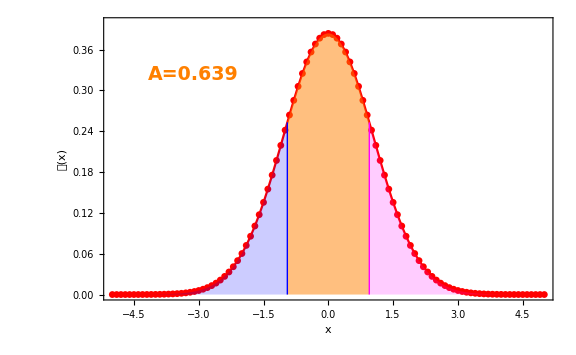

```mathematica
q=xargR[];r=limitsR[];Print[q," ",r[[1]]," ",r[[2]]];x0=-5;x1=5;shower[normalData[q,x0,x1],q,x0,r[[1]],x1,r[[2]]]
```

```mathematica
(*Manipulate[shower[normalData[{1,0},-5,5],{1,0},a,b],{a,-4,0,1},{b,0,4,1}]*)
```